94.6402

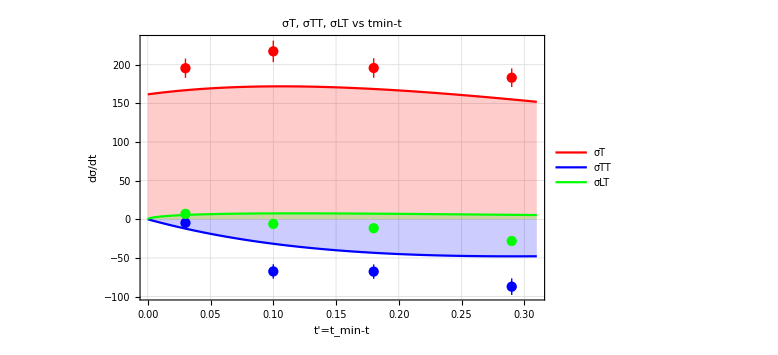
-Graphics- {Q2,xB}={3.11,0.36}

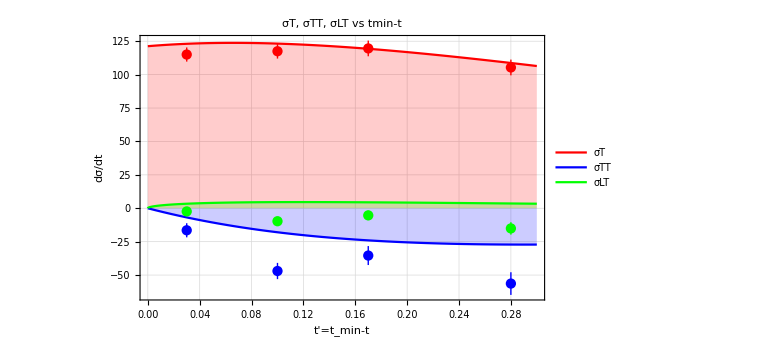
-Graphics- {Q2,xB}={3.57,0.36}

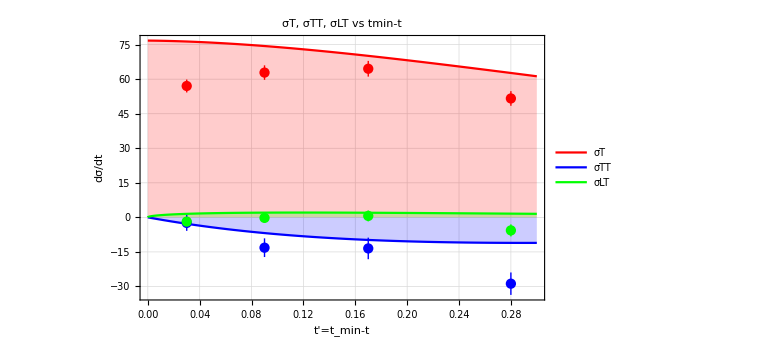
-Graphics- {Q2,xB}={4.44,0.36}

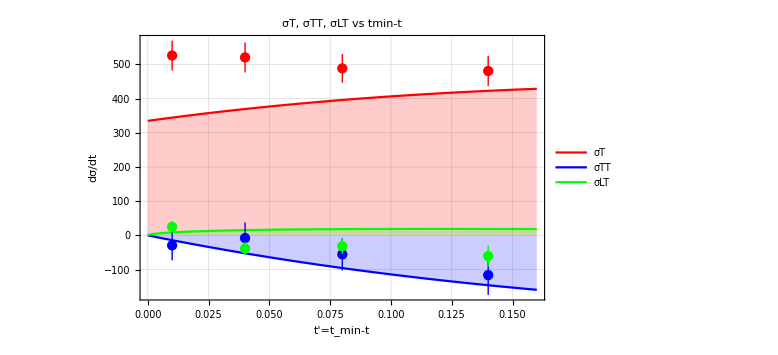
-Graphics- {Q2,xB}={2.67,0.48}

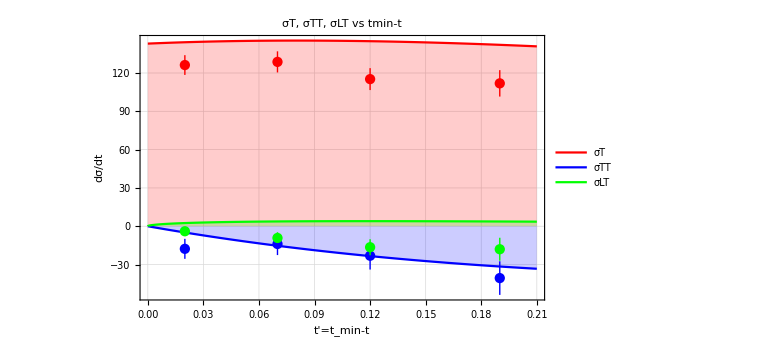
-Graphics- {Q2,xB}={4.05,0.48}

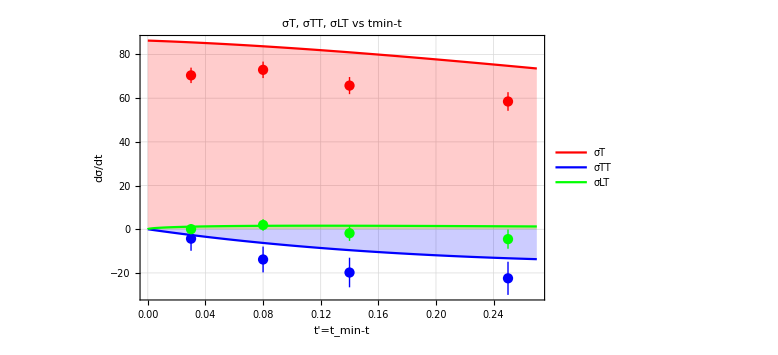
-Graphics- {Q2,xB}={5.16,0.48}

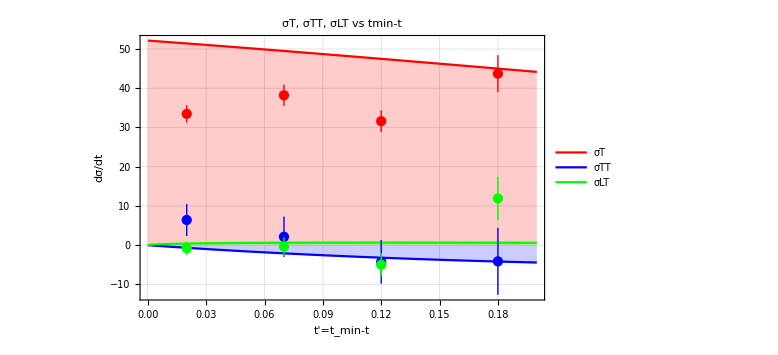
-Graphics- {Q2,xB}={6.56,0.48}

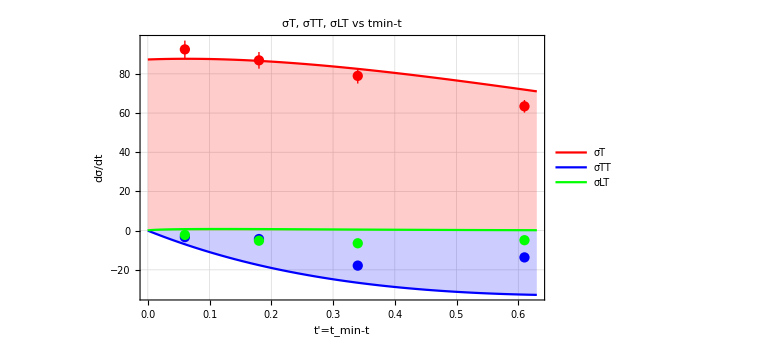
-Graphics- {Q2,xB}={5.49,0.6}

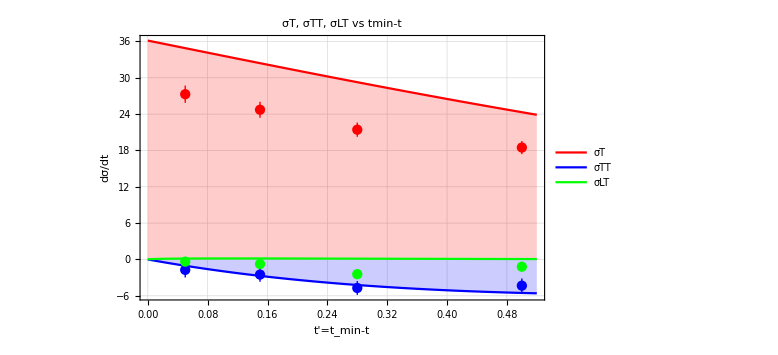
-Graphics- {Q2,xB}={8.31,0.6}

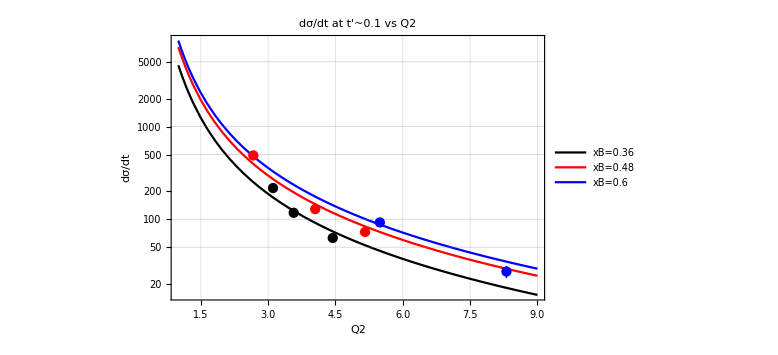

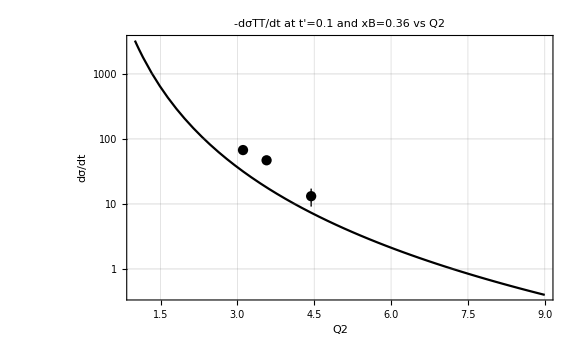

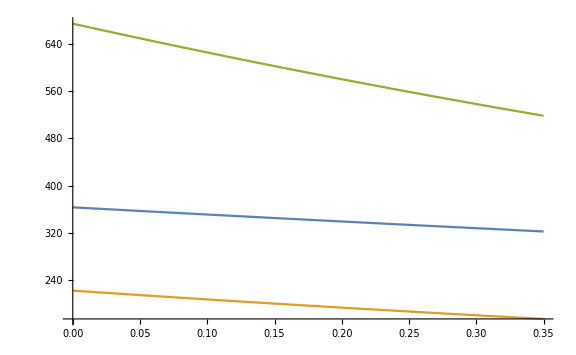

```mathematica
(* 
Data: 2020_11_20 HALL-A 2020 pi0 data arxiv: 2011.11125  Still unpublished.
Structure Functions (lines): vpk model (actually CLAS6 data)
*)

mpi0    = 0.1349764 ;
mp           = 0.93827231 ;
Ebeam      = 5.75;
Eb=Ebeam;

(*
* 6.2059,0.8019,-0.1064,1.8361,0.00,
* 94.6402,3.4433,-1.9773,-0.1315,0.0000,16.9977,2.1240,
*)
p1=6.2059;
p2=0.8019;
p3=-0.1064;
p4=1.836;
p5=0.0;

p6=94.6402 
p7=3.4433;
p8=-1.9773;
p9=-0.1315;
p10=0.0;
p11=16.9977;
p12=2.1240;

ALPHA=0.00729927;
Hc2=389379.36;
ksi[Q2_,x_]:=x/(2-x)*(1+mp^2/Q2);
W[Q2_,x_]:=Sqrt[Q2*(1/x-1)+mp^2];
E1CM[Q2_,x_]:=(W[Q2,x]^2+Q2+mp^2)/(2*W[Q2,x]);
E3CM[Q2_,x_]:=(W[Q2,x]^2-mpi0^2+mp^2)/(2*W[Q2,x]);
P1CM[Q2_,x_]:= Sqrt[E1CM[Q2,x]^2-mp^2];
P3CM[Q2_,x_]:= Sqrt[E3CM[Q2,x]^2-mp^2];
y[Q2_,x_,E_]:=Q2/(2*mp*x*E);
E1[Q2_,x_,E]:=Q2/(4*E^2);

tmin[Q2_,x_]:=-((Q2+mpi0^2)^2/4/W[Q2,x]^2-(P1CM[Q2,x]-P3CM[Q2,x])^2);
PHASE1[Q2_,x_]:=16*Pi*(W[Q2,x]^2-mp^2)*Sqrt[W[Q2,x]^4+Q2^2+mp^4+2*W[Q2,x]^2*Q2-2*W[Q2,x]^2*mp^2+2*Q2*mp^2];
PHASE2[Q2_,x_]:=16*Pi*(W[Q2,x]^2-mp^2)*Sqrt[W[Q2,x]^4+0.0     +mp^4+2*W[Q2,x]^2*Q2-2*W[Q2,x]^2*mp^2+2*Q2*mp^2];
PHASE[Q2_,x_]:=PHASE1[Q2,x];
HT[t_,Q2_,x_]:=p1*Exp[(p2+p3*(Log[x]-Log[0.15]))*t]*Q2^(p4/2.);
ET[t_,Q2_,x_]:=p6*Exp[(p7+p8*(Log[x]-Log[0.15]))*t]*Q2^(p9/2.);
HTEBAR[t_,Q2_,x_]:=p11*Exp[p12*t];

sTT[t_,Q2_,x_]:=If[-t>tmin[Q2,x],-Hc2*4*Pi*ALPHA/2/PHASE[Q2,x]/Q2^2*((-t-tmin[Q2,x])/8/mp^2*ET[t,Q2,x]^2),0.0];
(*sT[t_,Q2_,x_]:= If[-t>tmin[Q2,x]&&3.0>Q2>1.3&&x>0.09,    *)
sT[t_,Q2_,x_]:= If[-t>tmin[Q2,x]&&x>0.0,  Hc2*4*Pi*ALPHA/2/PHASE[Q2,x]/Q2^2*((1-ksi[Q2,x]^2)*HT[t,Q2,x]^2+(-t-tmin[Q2,x])/8/mp^2*ET[t,Q2,x]^2),.0];
sT1[t_,Q2_,x_]:= If[-t>tmin[Q2,x],    Hc2*4*Pi*ALPHA/2/PHASE[Q2,x]/Q2^2*((1-ksi[Q2,x]^2)*HT[t,Q2,x]^2+0*(-t-tmin[Q2,x])/8/mp^2*ET[t,Q2,x]^2),0.0];
sT2[t_,Q2_,x_]:= If[-t>tmin[Q2,x],    Hc2*4*Pi*ALPHA/2/PHASE[Q2,x]/Q2^2*(0*(1-ksi[Q2,x]^2)*HT[t,Q2,x]^2+(-t-tmin[Q2,x])/8/mp^2*ET[t,Q2,x]^2),0.0];
sLT[t_,Q2_,x_]:=If[-t>tmin[Q2,x],Hc2*4.*Pi*ALPHA/Sqrt[2.]/PHASE[Q2,x]/Q2^1.5*ksi[Q2,x]*Sqrt[1.-ksi[Q2,x]^2]*Sqrt[-t-tmin[Q2,x]]/2/mp*HTEBAR[t,Q2,x]^2,0.0];
sL[t_,Q2_,x_]:=0.0;
eps1[Q2_,x_,E_]:=(1-y[Q2,x,E]-Q2/(4*E^2))/(1-y[Q2,x,E]+y[Q2,x,E]^2/2+Q2/(4*E^2));
eps[Q2_,x_,E_]:=If[eps1[Q2,x,E]>0.0,(1-y[Q2,x,E]-Q2/(4*E^2))/(1-y[Q2,x,E]+y[Q2,x,E]^2/2+Q2/(4*E^2)),0.0];
sU[t_,Q2_,x_,E_]:=sT[t,Q2,x]+eps[Q2,x,E]*sL[t,Q2,x];
(*Plot[{sU[-t,2.,0.2,Ebeam]},{t,0.,2.}]*)
DataAll=
{{3.11,0.36,   0.,0.07,0.03,195.46,3.66,11.93,7.05,3.19,0.25,-4.66,7.62,0.16,14.52,6.91,0.51},{3.11,0.36,0.07,0.1,0.1,   217.29,4.22,13.26,-5.97,3.81,0.21,-67.45,9.03,2.36,18.91,8.05,0.66},{3.11,0.36,0.13,0.22,0.18,195.76,4.15,11.95,-11.55,4.01,0.4,-67.67,8.97,2.37,27.63,7.17,0.97},{3.11,0.36,0.22,0.38,0.29,183.18,4.54,11.18,-28.08,4.63,0.98,-87.12,10.23,3.05,9.05,6.38,0.32},{3.57,0.36,    0.,0.06,0.03,115.04,2.53,4.64,-2.37,2.18,0.08,-16.48,5.25,0.58,-5.08,4.97,0.18},{3.57,0.36,0.06,0.13,0.1, 117.51,2.77,4.74,-9.7,2.54,0.34,-46.96,5.85,1.64,18.11,5.31,0.63},{3.57,0.36,0.13,0.22,0.17,119.61,3.35,4.82,-5.32,3.52,0.19,-35.39,6.99,1.24,14.58,5.31,0.51},{3.57,0.36,0.22,0.35,0.28,105.37,4.06,4.25,-15.08,4.61,0.53,-56.36,8.24,1.97,10.04,4.88,0.35},{4.44,0.36,    0.,0.06,0.03,57.04,1.88,2.08,-1.84,1.44,0.06,-2.42,3.43,0.08,4.92,3.24,0.17},{4.44,0.36,0.06,0.13,0.09,62.86,2.16,2.29,-0.23,1.83,0.01,-13.17,4.03,0.46,5.04,3.63,0.18},{4.44,0.36,0.13,0.21,0.17,64.53,2.47,2.35,0.62,2.35,0.02,-13.49,4.66,0.47,6.39,3.65,0.22},{4.44,0.36,0.21,0.38,0.28,51.63,2.56,1.88,-5.66,2.61,0.2,-28.8,4.76,1.01,5.79,3.13,0.2},{2.67,0.48,    0.,0.03,0.01,525.95,14.48,41.16,25.07,16.53,0.88,-29.14,43.88,1.02,7.6,30.21,0.27},{2.67,0.48,0.03,0.06,0.04,520.4,16.36,40.73,-38.25,19.21,1.34,-7.88,45.79,0.28,-5.32,31.83,0.19},{2.67,0.48,0.06,0.11,0.08,488.33,17.33,38.22,-31.6,21.71,1.11,-55.44,47.02,1.94,16.7,28.69,0.5},{2.67,0.48,0.11,0.18,0.14,480.77,23.45,37.63,-60.2,30.66,2.11,-116.12,57.67,4.06,14.05,27.05,0.49},{4.05,0.48,    0.,0.05,0.02,126.23,3.84,6.71,-3.93,3.36,0.14,-17.69,7.8,0.62,16.81,8.43,0.59},{4.05,0.48,0.05,0.1,0.07,128.7,4.65,6.84,-9.18,4.45,0.32,-13.9,8.66,0.49,26.38,8.65,0.92},{4.05,0.48,0.1,0.16,0.12,115.22,6.01,6.12,-16.42,6.24,0.57,-23.1,10.78,0.81,30.12,8.41,1.05},{4.05,0.48,0.16,0.23,0.19,111.89,8.46,5.95,-18.01,8.97,0.63,-40.59,13.09,1.42,7.79,8.51,0.27},{5.16,0.48,    0.,0.05,0.03,70.45,2.53,2.47,0.04,2.23,0.,-4.31,5.55,0.15,2.63,4.28,0.09},{5.16,0.48,0.05,0.11,0.08,72.98,2.78,2.55,1.96,2.64,0.07,-13.84,5.89,0.46,7.15,4.4,0.25},{5.16,0.48,0.11,0.19,0.14,65.77,3.17,2.3,-1.82,3.51,0.06,-19.81,6.74,0.69,2.16,4.12,0.08},{5.16,0.48,0.19,0.33,0.25,58.49,3.74,2.05,-4.52,4.4,0.16,-22.46,7.55,0.79,6.62,3.53,0.23},{6.56,0.48,    0.,0.05,0.02,33.48,1.6,1.54,-0.79,1.73,0.03,6.43,4.08,0.23,3.23,2.96,0.11},{6.56,0.48,0.05,0.1,0.07,38.21,2.06,1.76,-0.39,2.39,0.01,2.15,5.14,0.08,0.98,3.3,0.03},{6.56,0.48,0.1,0.15,0.12,31.61,2.35,1.46,-4.97,2.95,0.17,-4.24,5.56,0.15,10.66,3.11,0.37},{6.56,0.48,0.15,0.21,0.18,43.74,4.23,2.02,11.91,5.51,0.42,-4.12,8.54,0.14,6.22,3.39,0.22},{5.49,0.6,      0.,0.12,0.06,92.48,1.42,4.26,-2.18,0.7,0.44,-3.29,1.67,0.12,6.61,1.68,0.23},{5.49,0.6,0.12,0.26,0.18,86.89,1.39,4.01,-5.12,0.75,1.04,-4.28,1.66,0.15,6.47,1.6,0.23},{5.49,0.6,0.26,0.44,0.34,78.96,1.38,3.64,-6.44,0.86,1.31,-17.84,1.74,0.62,5.47,1.47,0.19},{5.49,0.6,0.44,0.88,0.61,63.43,1.37,2.92,-4.87,1.03,0.99,-13.65,1.82,0.48,6.66,1.1,0.23},{8.31,0.6,    0.,0.09,0.05,27.29,0.9,1.1,-0.36,0.48,0.01,-1.72,1.25,0.06,1.18,0.9,0.04},{8.31,0.6,0.09,0.21,0.15,24.72,0.86,1.,-0.75,0.48,0.03,-2.5,1.18,0.09,1.7,0.83,0.06},{8.31,0.6,0.21,0.36,0.28,21.43,0.81,0.86,-2.43,0.49,0.09,-4.71,1.13,0.16,0.21,0.71,0.01},{8.31,0.6,0.36,0.69,0.5,18.48,0.79,0.74,-1.2,0.58,0.04,-4.33,1.18,0.15,3.1,0.56,0.11}};
(*        dsigma/dt    *)
plotn[n_]:=
Module[{n0},
n0=n; n1=n0+1; n2=n0+2; n3=n0+3;
tprim1=Extract[Extract[DataAll,{n0}],{5}];
tprim2=Extract[Extract[DataAll,{n1}],{5}];
tprim3=Extract[Extract[DataAll,{n2}],{5}];
tprim4=Extract[Extract[DataAll,{n3}],{5}];
sU1=Extract[Extract[DataAll,{n0}],{6}];
sU2=Extract[Extract[DataAll,{n1}],{6}];
sU3=Extract[Extract[DataAll,{n2}],{6}];
sU4=Extract[Extract[DataAll,{n3}],{6}];
dsU1=Sqrt[Extract[Extract[DataAll,{n0}],{7}]^2 + Extract[Extract[DataAll,{n0}],{8}]^2];
dsU2=Sqrt[Extract[Extract[DataAll,{n1}],{7}]^2 + Extract[Extract[DataAll,{n1}],{8}]^2];
dsU3=Sqrt[Extract[Extract[DataAll,{n2}],{7}]^2 + Extract[Extract[DataAll,{n2}],{8}]^2];
dsU4=Sqrt[Extract[Extract[DataAll,{n3}],{7}]^2 + Extract[Extract[DataAll,{n3}],{8}]^2];
sLT1=Extract[Extract[DataAll,{n0}],{9}];
sLT2=Extract[Extract[DataAll,{n1}],{9}];
sLT3=Extract[Extract[DataAll,{n2}],{9}];
sLT4=Extract[Extract[DataAll,{n3}],{9}];
dsLT1=Sqrt[Extract[Extract[DataAll,{n0}],{10}]^2 + Extract[Extract[DataAll,{n0}],{11}]^2];
dsLT2=Sqrt[Extract[Extract[DataAll,{n1}],{10}]^2 + Extract[Extract[DataAll,{n1}],{11}]^2];
dsLT3=Sqrt[Extract[Extract[DataAll,{n2}],{10}]^2 + Extract[Extract[DataAll,{n2}],{11}]^2];
dsLT4=Sqrt[Extract[Extract[DataAll,{n3}],{10}]^2 + Extract[Extract[DataAll,{n3}],{11}]^2];
sTT1=Extract[Extract[DataAll,{n0}],{12}];
sTT2=Extract[Extract[DataAll,{n1}],{12}];
sTT3=Extract[Extract[DataAll,{n2}],{12}];
sTT4=Extract[Extract[DataAll,{n3}],{12}];
dsTT1=Sqrt[Extract[Extract[DataAll,{n0}],{13}]^2 + Extract[Extract[DataAll,{n0}],{14}]^2];
dsTT2=Sqrt[Extract[Extract[DataAll,{n1}],{13}]^2 + Extract[Extract[DataAll,{n1}],{14}]^2];
dsTT3=Sqrt[Extract[Extract[DataAll,{n2}],{13}]^2 + Extract[Extract[DataAll,{n2}],{14}]^2];
dsTT4=Sqrt[Extract[Extract[DataAll,{n3}],{13}]^2 + Extract[Extract[DataAll,{n3}],{14}]^2];

sUpoints={ {tprim1,Around[sU1,dsU1]},{tprim2,Around[sU2,dsU2]},{tprim3,Around[sU3,dsU3]},{tprim4,Around[sU4,dsU4]} };
sTTpoints={ {tprim1,Around[sTT1,dsTT1]},{tprim2,Around[sTT2,dsTT2]},{tprim3,Around[sTT3,dsTT3]},{tprim4,Around[sTT4,dsTT4]} };
sLTpoints={ {tprim1,Around[sLT1,dsLT1]},{tprim2,Around[sLT2,dsLT2]},{tprim3,Around[sLT3,dsLT3]},{tprim4,Around[sLT4,dsLT4]} };

(*        dsigma/dQ2    *)

Q21=Extract[Extract[DataAll,{2}],{1}];
Q22=Extract[Extract[DataAll,{6}],{1}];
Q23=Extract[Extract[DataAll,{10}],{1}];
Q24=Extract[Extract[DataAll,{14}],{1}];
sTT1Q=-Extract[Extract[DataAll,{2}],{12}];
sTT2Q=-Extract[Extract[DataAll,{6}],{12}];
sTT3Q=-Extract[Extract[DataAll,{10}],{12}];
sTT4Q=-Extract[Extract[DataAll,{14}],{12}];
dsTT1Q=Sqrt[Extract[Extract[DataAll,{2}],{13}]^2 + Extract[Extract[DataAll,{2}],{14}]^2];
dsTT2Q=Sqrt[Extract[Extract[DataAll,{6}],{13}]^2 + Extract[Extract[DataAll,{6}],{14}]^2];
dsTT3Q=Sqrt[Extract[Extract[DataAll,{10}],{13}]^2 + Extract[Extract[DataAll,{10}],{14}]^2];
dsTT4Q=Sqrt[Extract[Extract[DataAll,{14}],{13}]^2 + Extract[Extract[DataAll,{14}],{14}]^2];
sTTpointsQ={ {Q21,Around[sTT1Q,dsTT1Q]},{Q22,Around[sTT2Q,dsTT2Q]},{Q23,Around[sTT3Q,dsTT3Q]}};

sT1Q=Extract[Extract[DataAll,{2}],{6}];
sT2Q=Extract[Extract[DataAll,{6}],{6}];
sT3Q=Extract[Extract[DataAll,{10}],{6}];
dsT1Q=Sqrt[Extract[Extract[DataAll,{2}],{7}]^2 + Extract[Extract[DataAll,{2}],{8}]^2];
dsT2Q=Sqrt[Extract[Extract[DataAll,{6}],{7}]^2 + Extract[Extract[DataAll,{6}],{8}]^2];
dsT3Q=Sqrt[Extract[Extract[DataAll,{10}],{7}]^2 + Extract[Extract[DataAll,{10}],{8}]^2];
sTpointsQ={ {Q21,Around[sT1Q,dsT1Q]},{Q22,Around[sT2Q,dsT2Q]},{Q23,Around[sT3Q,dsT3Q]}};

Q212=Extract[Extract[DataAll,{15}],{1}];
Q222=Extract[Extract[DataAll,{18}],{1}];
Q232=Extract[Extract[DataAll,{22}],{1}];
sT1Q2=Extract[Extract[DataAll,{15}],{6}];
sT2Q2=Extract[Extract[DataAll,{18}],{6}];
sT3Q2=Extract[Extract[DataAll,{22}],{6}];
dsT1Q2=Sqrt[Extract[Extract[DataAll,{15}],{7}]^2 + Extract[Extract[DataAll,{15}],{8}]^2];
dsT2Q2=Sqrt[Extract[Extract[DataAll,{18}],{7}]^2 + Extract[Extract[DataAll,{18}],{8}]^2];
dsT3Q2=Sqrt[Extract[Extract[DataAll,{22}],{7}]^2 + Extract[Extract[DataAll,{22}],{8}]^2];
sTpointsQ2={ {Q212,Around[sT1Q2,dsT1Q2]},{Q222,Around[sT2Q2,dsT2Q2]},{Q232,Around[sT3Q2,dsT3Q2]}};

Q213=Extract[Extract[DataAll,{29}],{1}];
Q223=Extract[Extract[DataAll,{33}],{1}];
sT1Q3=Extract[Extract[DataAll,{29}],{6}];
sT2Q3=Extract[Extract[DataAll,{33}],{6}];
dsT1Q3=Sqrt[Extract[Extract[DataAll,{29}],{7}]^2 + Extract[Extract[DataAll,{27}],{8}]^2];
dsT2Q3=Sqrt[Extract[Extract[DataAll,{33}],{7}]^2 + Extract[Extract[DataAll,{30}],{8}]^2];
sTpointsQ3={ {Q213,Around[sT1Q3,dsT1Q3]},{Q223,Around[sT2Q3,dsT2Q3]}};

(*        PLOTs dσ/dt    *)
QQ2=Extract[Extract[DataAll,{n0}],{1}];
xB=Extract[Extract[DataAll,{n0}],{2}];
tmx=Extract[Extract[DataAll,{n3}]+0.02,{5}];
Show[
Plot[{sT[-tm-tmin[QQ2,xB],QQ2,xB],sTT[-tm-tmin[QQ2,xB],QQ2,xB],sLT[-tm-tmin[QQ2,xB],QQ2,xB]},{tm,0.0,tmx},
Frame->True,Filling->Axis,PlotStyle->{Red,Blue,Green,Magenta},ImageSize->Large,BaseStyle->{FontSize->16},
GridLines->Automatic,PlotRange->All,
PlotLegends->Placed[{"σT","σTT","σLT"},Right],
PlotLabel->Style["σT, σTT, σLT vs tmin-t",Black,Bold,18],
FrameLabel->{"t'=t_min-t","dσ/dt"}
],
ListPlot[sUpoints,PlotStyle->{Red}],
ListPlot[sTTpoints,PlotStyle->{Blue}],
ListPlot[sLTpoints,PlotStyle->{Green}]]];

plotn[1]   Row[Style[#,Blue,22]&/@{"{Q2,xB}=",{QQ2,xB}}] 
plotn[5]    Row[Style[#,Blue,22]&/@{"{Q2,xB}=",{QQ2,xB}}] 
plotn[9]   Row[Style[#,Blue,22]&/@{"{Q2,xB}=",{QQ2,xB}}] 
plotn[13]    Row[Style[#,Blue,22]&/@{"{Q2,xB}=",{QQ2,xB}}] 
plotn[17]   Row[Style[#,Blue,22]&/@{"{Q2,xB}=",{QQ2,xB}}] 
plotn[21]    Row[Style[#,Blue,22]&/@{"{Q2,xB}=",{QQ2,xB}}] 
plotn[25]   Row[Style[#,Blue,22]&/@{"{Q2,xB}=",{QQ2,xB}}] 
plotn[29]    Row[Style[#,Blue,22]&/@{"{Q2,xB}=",{QQ2,xB}}] 
plotn[33]    Row[Style[#,Blue,22]&/@{"{Q2,xB}=",{QQ2,xB}}] 

(*        PLOTs dσ/dQ2    *)
Show[
LogPlot[{sT[-0.1-tmin[QQ2,0.36],QQ2,0.36],sT[-0.08-tmin[QQ2,0.48],QQ2,0.48],sT[-0.05-tmin[QQ2,0.6],QQ2,0.6]},{QQ2,1,9},
GridLines->Automatic,Axes->True,
Frame->True,PlotStyle->{Black,Red,Blue},
PlotLegends->Placed[{"xB=0.36","xB=0.48","xB=0.6"},Right],
PlotLabel->Style["dσ/dt at t'~0.1 vs Q2",Black,Bold,18],
FrameLabel->{"Q2","dσ/dt"},
ImageSize->Large,BaseStyle->{FontSize->16}],
ListLogPlot[sTpointsQ,PlotStyle->{Black}],
ListLogPlot[sTpointsQ2,PlotStyle->{Red}],
ListLogPlot[sTpointsQ3,PlotStyle->{Blue}]
]

Show[
LogPlot[{-sTT[-0.1-tmin[QQ2,0.36],QQ2,0.36]},{QQ2,1,9},
GridLines->Automatic,Axes->True,
PlotLabel->Style["-dσTT/dt at t'=0.1 and xB=0.36 vs Q2",Black,Bold,18],
Frame->True,PlotStyle->{Red,Blue,Black},
FrameLabel->{"Q2","dσ/dt"},
ImageSize->Large,BaseStyle->{FontSize->16}],
ListLogPlot[sTTpointsQ,PlotStyle->{Black}]
]

sUA[QQ2_,tp_,C_,A_,B_]:=C QQ2^A Exp[-B tp];
Plot[{
sUA[3.11,tp,8.6,3.3,0.34],
sUA[3.11,tp,8.3,2.9,0.69],
sUA[3.11,tp,20.,3.1,0.75]},
{tp,0,0.35}]
```